```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/phasedata_v2/datav2

```mathematica
chi0=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi0.dat"]],{i,700,870,5}];
chi1=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi1.dat"]],{i,700,870,5}];
chi2=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi2.dat"]],{i,700,870,5}];
chi3=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi3.dat"]],{i,700,870,5}];
chi4=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi4.dat"]],{i,700,870,5}];
r42=chi4/chi2//Quiet;
r21=chi2/chi1//Quiet;
r12=chi1/chi2//Quiet;
r32=chi3/chi2//Quiet;
r31=chi3/chi1//Quiet;
```

```mathematica
r42[[1;;45]][[1;;60]]=1;
```

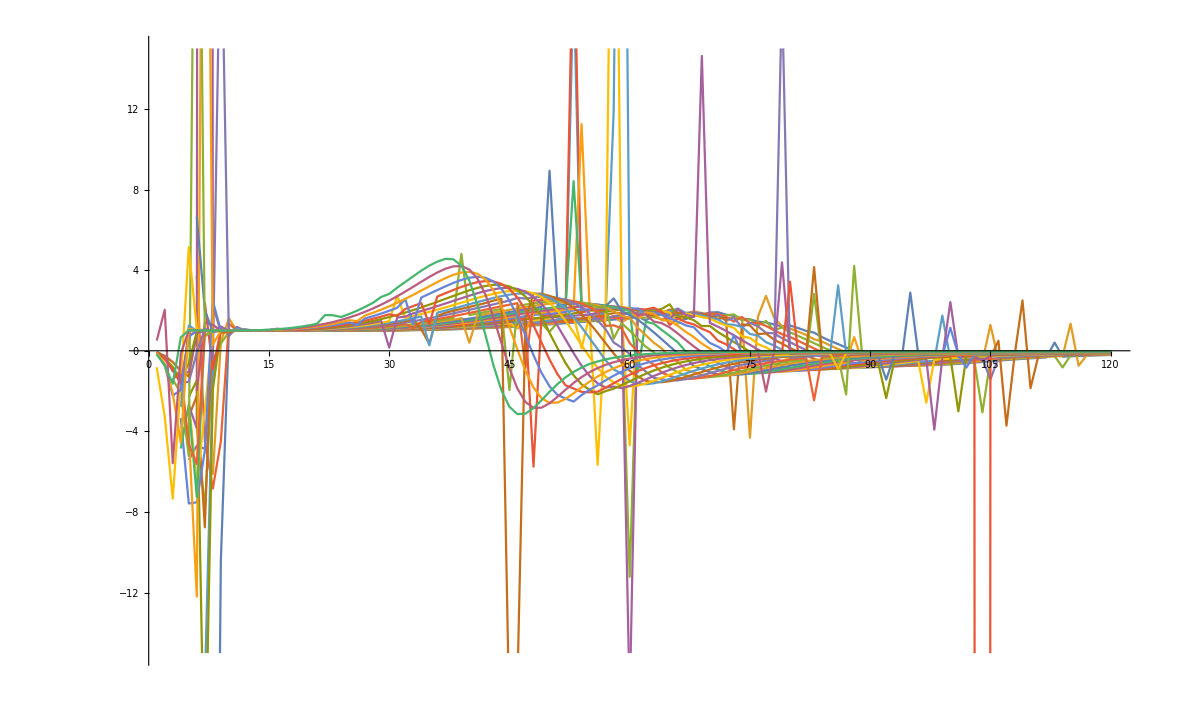

```mathematica
ListLinePlot[Table[r42[[i]],{i,1,30}],PlotRange->{All,{-15,15}}]
```

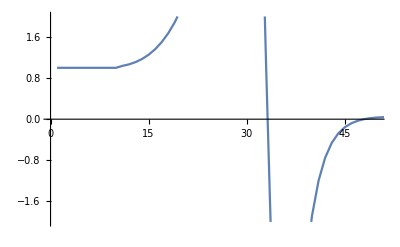

```mathematica
ListLinePlot[r42[[88]],PlotRange->{{0,50},{-2,2}}]
```

```mathematica
mub=Table[i,{i,0,870,10}];
T=Table[i,{i,1,120,1}];
```

```mathematica
R42all=Flatten[Table[{x=mub[[j]],y=T[[i]],r42[[j]][[i]]},{i,1,120},{j,1,88}],1];
Export["r42low.dat",R42all]
```

Part::partd: 部分指定 1⟦1⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

r42low.dat

```mathematica
ListDensityPlot[R42all,PlotRange->{All,All,{-5,5}}]
```

Part::partd: 部分指定 1.⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 1.⟦2⟧ 比对象深度更长.

Part::partd: 部分指定 1.⟦3⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

-Graphics-

```mathematica
R21all=Flatten[Table[{x=mub[[j]],y=T[[i]],-r21[[j]][[i]]},{i,1,120},{j,1,88}],1];
Export["r21low.dat",R21all]
R12all=Flatten[Table[{x=mub[[j]],y=T[[i]],-r12[[j]][[i]]},{i,1,120},{j,1,88}],1];
Export["r12low.dat",R12all]
R32all=Flatten[Table[{x=mub[[j]],y=T[[i]],-r32[[j]][[i]]},{i,1,120},{j,1,88}],1];
Export["r32low.dat",R32all]
R31all=Flatten[Table[{x=mub[[j]],y=T[[i]],r31[[j]][[i]]},{i,1,120},{j,1,88}],1];
Export["r31low.dat",R31all]
chi2all=Flatten[Table[{x=mub[[j]],y=T[[i]],chi2[[j]][[i]]},{i,1,120},{j,1,88}],1];
Export["chi2low.dat",chi2]
```

Part::partd: 部分指定 mub⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 T⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 mub⟦2⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

r21low.dat

Part::partd: 部分指定 mub⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 T⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 mub⟦2⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

r12low.dat

Part::partd: 部分指定 mub⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 T⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 mub⟦2⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

r32low.dat

Part::partd: 部分指定 mub⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 T⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 mub⟦2⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

r31low.dat

Part::partd: 部分指定 mub⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 T⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 mub⟦2⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

chi2low.dat